```mathematica
f[X_] := (2n m Sinh[m X β])/(1+2Cosh[m X β])
FullSimplify[f'[x]]
```

(2 m^2 n β (2+Cosh[m x β]))/(1+2 Cosh[m x β])^2

```mathematica
TrigReduce[(2 m Cosh[m x])/(1+2 Cosh[m x])-(4 m Sinh[m x]^2)/(1+2 Cosh[m x])^2]
```

(2 (m+m Cosh[m x]+2 m Cosh[m x]^2-m Cosh[2 m x]))/(1+2 Cosh[m x])^2

1

-1

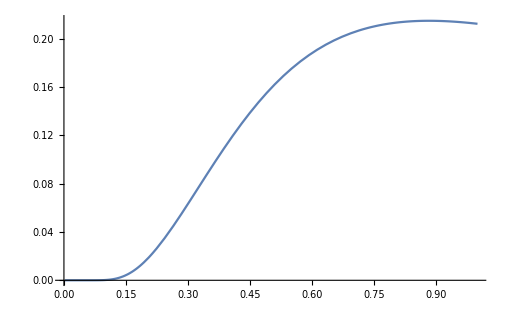

```mathematica
h = 1
h2 = -1
Plot[{1/X(2+Cosh[h/X])/(1+2 Cosh[h/X])^2},{X,0,1}]
```

```mathematica
Cosh[0]
```

1

```mathematica
Cosh[1]
```

Cosh[1]

```mathematica
N[Cosh[1]]
```

1.54308

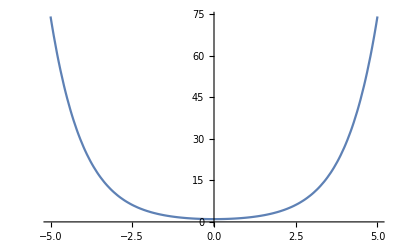

```mathematica
Plot[Cosh[x],{x,-5,5}]
```

```mathematica
Integrate[1/Sinh[x/2],{x,Subscript[ϕ, 0], ϕ}]
```

ConditionalExpression[-2 Log[Coth[ϕ/4] Tanh[ϕ_0/4]],Sinh[ϕ/4]≥0&&Cosh[ϕ_0/4]≥0&&Sinh[ϕ_0/4]≥0&&Cosh[ϕ/4]≥0]

```mathematica
TrigToExp[2 (Log[Cosh[ϕ/4]]-Log[Sinh[ϕ/4]])]
```

-2 Log[1/2 (-ⅇ^(-ϕ/4)+ⅇ^(ϕ/4))]+2 Log[1/2 (ⅇ^(-ϕ/4)+ⅇ^(ϕ/4))]

```mathematica
-2 Log[Coth[ϕ/4] Tanh[Subscript[ϕ, 0]/4]]
```

-2 Log[Coth[ϕ/4] Tanh[ϕ_0/4]]

```mathematica
Integrate[1/Sinh[x/2],x]
```

-2 Log[Cosh[x/4]]+2 Log[Sinh[x/4]]

```mathematica
Integrate[ⅇ^u,{u,a,b}]
```

-ⅇ^a+ⅇ^b

```mathematica
f[x_] := -Nm Log[(8 π)/(J x)Sinh[J x/2]]
Simplify[f'[x]]
```

Nm/x-1/2 J Nm Coth[(J x)/2]

```mathematica
Simplify[(J x Csch[(J x)/2] ((4 π Cosh[(J x)/2])/x-(8 π Sinh[(J x)/2])/(J x^2)))/(8 π)]
```

-1/x+1/2 J Coth[(J x)/2]

```mathematica
g[x_]:= Nm/x-1/2 J Nm Coth[(J x)/2]
Simplify[g'[x]]
```

-Nm/x^2+1/4 J^2 Nm Csch[(J x)/2]^2

```mathematica
Integrate[1/(2 Sinh[x/2]),{x,Subscript[ϕ, 0], ϕ}]
```

ConditionalExpression[-Log[Coth[ϕ/4] Tanh[ϕ_0/4]],Sinh[ϕ/4]≥0&&Cosh[ϕ_0/4]≥0&&Sinh[ϕ_0/4]≥0&&Cosh[ϕ/4]≥0]

```mathematica
FullSimplify[-Log[Coth[ϕ/4] Tanh[Subscript[ϕ, 0]/4]]]
```

-Log[Coth[ϕ/4] Tanh[ϕ_0/4]]

```mathematica
TrigToExp[-Log[Coth[ϕ/4] Tanh[Subscript[ϕ, 0]/4]]]
```

-Log[((ⅇ^(-ϕ/4)+ⅇ^(ϕ/4)) (-ⅇ^(-ϕ_0/4)+ⅇ^(ϕ_0/4)))/((-ⅇ^(-ϕ/4)+ⅇ^(ϕ/4)) (ⅇ^(-ϕ_0/4)+ⅇ^(ϕ_0/4)))]

```mathematica
Simplify[-Log[((ⅇ^(-ϕ/4)+ⅇ^(ϕ/4)) (-ⅇ^(-Subscript[ϕ, 0]/4)+ⅇ^(Subscript[ϕ, 0]/4)))/((-ⅇ^(-ϕ/4)+ⅇ^(ϕ/4)) (ⅇ^(-Subscript[ϕ, 0]/4)+ⅇ^(Subscript[ϕ, 0]/4)))]]
```

-Log[((1+ⅇ^(ϕ/2)) (-1+ⅇ^(ϕ_0/2)))/((-1+ⅇ^(ϕ/2)) (1+ⅇ^(ϕ_0/2)))]

```mathematica
Integrate[(2 a x)/(ⅇ^x-1),{x,-a,∞}]
```

a^3+(2 a π^2)/3+2 a^2 Log[1-ⅇ^-a]-2 a PolyLog[2,ⅇ^-a]

```mathematica
Integrate[a^2/(ⅇ^x-1),{x,-a,∞}]
```

-a^2 (a-ⅈ π+Log[1-ⅇ^-a])

```mathematica
PolyLog
```

```mathematica
Integrate[(x+β μ)^2/(ⅇ^x-1),{x,-β μ, ∞}]
```

∫_(-β μ)^∞ (x+β μ)^2/(-1+ⅇ^x)ⅆx

```mathematica
Assuming[Re[β]>0,Integrate[x^2/(ⅇ^(β(x-μ))-1),{x,0, ∞}]]
```

```mathematica
(2 PolyLog[3,ⅇ^(β μ)])/β^3
```

(2 PolyLog[3,ⅇ^(β μ)])/β^3

```mathematica
Integrate[1/Sinh[x/2],{x,ϕ0, ϕ}]
```

ConditionalExpression[-2 Log[Coth[ϕ/4] Tanh[ϕ0/4]],Sinh[ϕ/4]≥0&&Cosh[ϕ0/4]≥0&&Sinh[ϕ0/4]≥0&&Cosh[ϕ/4]≥0]

0.5

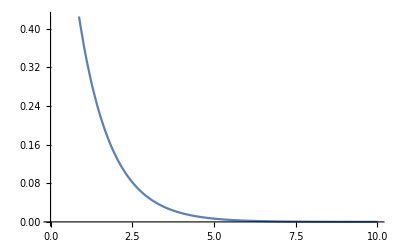

```mathematica
B = .5
Plot[Log[(1+B ⅇ^-x)/(1-B ⅇ^-x)],{x,0,10}]
```

```mathematica
((6.626*10^-27)^2)/(2 π 37 * 1.6726*10^-24 1.3807*10^-16)(2.5*10^12/2.612)^(2/3)
```

7.9422×10^-8

```mathematica
1.05*750*10^-27
```

7.875×10^-25

```mathematica
1.3807*10^-16*170*10^-9
```

2.34719×10^-23

```mathematica
ℏ = 1.05*10^-27;
ω0 = 750;
ω1 = 265;
kb = 1.3807*10^-16;
Nmax = 2*10^4;
((Sqrt[3]2.404/2)/(ℏ^3 ω0 ω1^2 Nmax))^(-1/3)kb
```

1.6502×10^7